## Логистическая регрессия и регуляризация.

##### Постановка задачи.

Задано множество объектов X, существует множество ответов Y={0,1} - бинарное множество  и существует целевая функция y^*:X→Y, значения которой y_i=y^*(x_i) известны только на конечном подмножестве объектов {x_1,...,x_l}⊂X.

Требуется по заданному множеству пар объект-ответ восстановить классифицирующую функцию a(x):X→ Y.

Определим вид функции a(x):

a(x,θ)=(1+ⅇ^-θᵀx)^-1

Метод логистической регрессии имеет ряд особенностей, одна из которых - возникновение возможности на ряду с классификацией объекта получать численные оценки вероятности его принадлежности каждому из классов.

Значение функции a(x,θ) будем определять как вероятность принадлежности объекта x к классу y=1:

p(+1|x,θ)=a(x,θ),
 p(0|x,θ)=1-a(x,θ).

Так как функция a(0,0)=0.5, т.е. 50%, это означает, что  уравнение θᵀx=0 задает разделяющую поверхность между двумя классами.

Отступом будем называть величину ошибки алгоритма на объекте x или дальность его расположения от разделяющей поверхности. В случае когда множество ответов может иметь значение 0 или 1, отступ определяется следующим образом:

M(θ,x,y)=y (θᵀx)+(y-1)(θᵀx)

Теперь можно определить вид функции потерь. Функция потерь это та функция, которая определяет величину штрафа за неправильную классификацию объекта х (отступ M<0 ) или за его слишком близкое нахождение к границе класса (M≈0). В случае логистической регрессии, функция потерь имеет вид:

L(M)=ln(1+ⅇ^-M)

После того, как мы определили функцию потерь, можно определить функционал качества - средняя ошибка на всей выборке:

Q(θ)=1/(2l)∑_(i=1)^l L(M(θ,x^(i),y^(i)))

Тогда для нахождения решающей функции a(x,θ), необходимо решить задачу оптимизации:

a(x,θ), где θ=arg min_θ Q(θ)

Решение задачи оптимизации будем проводить методом градиентного спуска:

θ_j^(k+1)=θ_j^k-α∂/(∂θ_i)Q(θ^k),
где ∂/(∂θ_i)Q(θ)=1/(2l)(∑∂/(∂θ_i))_(i=1)^l L(M(θ,x^(i),y^(i)))=1/(2l)∑_(i=1)^l L'(M(θ,x^(i),y^(i)))(2 y^(i)-1)x_j^(i),

α- скорость обучения.

Дополнительно рассмотрим проблему переобучения.

Переобучение - явление, при котором решающая функция подстраивается под обучающую выборку настолько, что теряет способность обобщать и становится слишком уязвимой для шумов.

Для предотвращения переобучения можно ввести дополнительное ограничение на размер θ_i:

Q(θ)=1/(2l)∑_(i=1)^l L(M(θ,x^(i),y^(i)))+λ/(2m)∑_(i=1)^n θ_i^2

Тогда градиентный шаг будет высчитываться по формуле:

θ_j^(k+1)=θ_j^k(1-α λ/l) -α∂/(∂θ_i)Q(θ)

Примечание: Условие малости не накладывается на коэффициент θ_0.

Рассмотрим пример:

##### Пример

Пусть у нас имеется обучающее множество объектов data:

```mathematica
data=Import["C:\\Users\\xx\\Desktop\\machine-learning-ex2\\ex2\\ex2data2.txt","Data"];
```

Объект data[[i]] имеет следующий вид:

```mathematica
data[[1]]
```

{0.051267,0.69956,1}

Где его первый элемент - это признак x_1, второй элемент - признак x_2, третий элемент - класс этого объекта.

Проиллюстрируем на плоскости распределение объектов. Для этого разделим множество data на X1 и X2, где Х1 - множество объектов первого класса,Х1 - множество объектов второго класса.

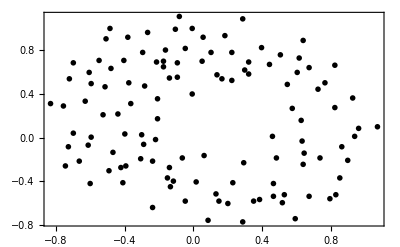

```mathematica
X1=Select[data,#[[3]]==0&][[;;,{1,2}]];
X2=Select[data,#[[3]]==1&][[;;,{1,2}]];
ListPlot[{X1,X2},PlotStyle->{PointSize[1]},Frame->True,ImageSize->400,Axes->False]
```

Из данной диаграммы видно, через обучающую выборку провести линейную границу невозможно. Следовательно необходимо введение дополнительных признаков x_1^2,x_1 x_2,... и т.д.

Составим комбинацию признаков x_1 и x_2 вплоть до шестой степени следующим образом:

```mathematica
x1x2=Flatten@{1,Table[#1^(i-j)*#2^j,{i,1,6},{j,0,i}]}&[x1,x2]
```

{1,x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4,x1^5,x1^4 x2,x1^3 x2^2,x1^2 x2^3,x1 x2^4,x2^5,x1^6,x1^5 x2,x1^4 x2^2,x1^3 x2^3,x1^2 x2^4,x1 x2^5,x2^6}

Данная комбинация признаков позволит нам задавать сложные разделяющие поверхности.

Отсортируем множество объектов data по их классу:

```mathematica
data=SortBy[data,Last];
```

Запишем множества X,Y - множество признаком объектов, множество классов объектов.

```mathematica
Y=data[[;;,3]];
XX=Table[Flatten@{1,data[[i,{1,2}]]},{i,1,Length[data]}];
```

Теперь составим комбинацию каждого i_ого признака по образцу записанному выше:

```mathematica
X=Table[Flatten@{1,Table[(data[[k]][[1]])^(i-j)*(data[[k]][[2]])^j,{i,1,6},{j,0,i}]},{k,1,Length[data]}];
```

Зададим функцию отступа, потерь и средний функционал качества:

```mathematica
M[w_,x_,y_]:=w.x*y+w.x(y-1)
L[m_]:=Log[1+Exp[-m]]
dL[m_]:=-ⅇ^-m/(1+ⅇ^-m)
Q[w_,λ_]:=1/(2Length[X])(Sum[L[M[w,X[[i]],Y[[i]]]],{i,1,Length[X]}]+λ Sum[w[[i]]^2,{i,2,Length[w]}])
```

Теперь составим алгоритм градиентного спуска:

```mathematica
GradDecent[X_,Y_,a_,λ_,maxiter_]:=Module[{w=RandomReal[{-.1,.1},Length[X[[1]]]],m=Length[X],i,j,t1={},w1},
AppendTo[t1,w];
For[i=1,i≤maxiter,i++,
w1=w(1-(a λ)/m)-a/m Sum[dL[M[w,X[[j]],Y[[j]]]](2Y[[j]]-1)X[[j]],{j,1,m}];
w=w1;
AppendTo[t1,w];];
{w,t1}]
```

Примечание: также на каждой итерации будем записывать значение вектора весов.

Сначала рассмотрим случай отсутствия регуляризации:

```mathematica
θ1=GradDecent[X,Y,9,0,10000];
```

Для контроля, изобразим график зависимости значения функционала качества от числа итераций:

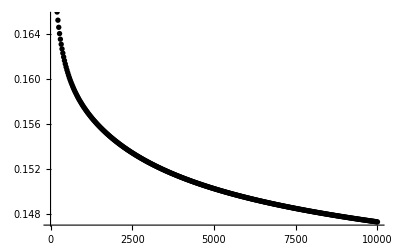

```mathematica
ListPlot[Table[{i,Q[θ1[[2]][[i]],0]},{i,1,Length[θ1[[2]]],25}],PlotMarkers->{Automatic,5.5},ImageSize->400]
```

Уменьшение функционала качества является подтверждением того, что алгоритм работает верно, но судя по наклону данной кривой, алгоритм за десять тысяч итераций так и не достиг точки глобального минимума.

Существует множество более эффективных алгоритмов оптимизации (стохастический градиент, метод Ньютона второго порядка и т.д.) но рассматривать их сейчас мы не будем. Вместо этого воспользуемся встроенной функцией численной оптимизации NArgMin:

```mathematica
θ[l_]:=NArgMin[Q[Table[w[i],{i,1,28}],l],Table[w[i],{i,1,28}]]
```

Случай когда θ=θ(0) соответствует отсутствию регуляризации. Посмотрим на конечный вектор весов:

```mathematica
θ[0]
```

{38.2244,55.5866,98.1265,-369.368,-177.092,-194.226,-365.95,-842.044,-719.304,-511.785,1182.51,1279.13,1907.56,914.156,514.18,573.134,1629.45,2553.11,2918.47,1780.24,785.149,-1257.72,-2259.62,-4142.04,-4289.78,-4228.85,-2055.15,-750.229}

Как мы видим, модули компонент вектора весов принимают большие значения. Изобразим разделяющую границу, которая соответствует данному вектору весов:

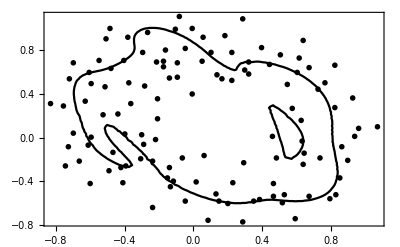

```mathematica
Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Axes->False,Frame->True,ImageSize->400],ContourPlot[Evaluate[θ[0].x1x2==0],{x1,-2,2},{x2,-2,2}]]
```

Данный пример наглядно демонстрирует эффект переобучения: граница слишком волнистая, шумы создают вокруг себя дополнительные области. К счастью, как уже было сказано раннее, регуляризация устраняет данный недостаток логистической регрессии.

Рассмотрим 4 примера, в которых λ={0.01,0.1,1,10}:

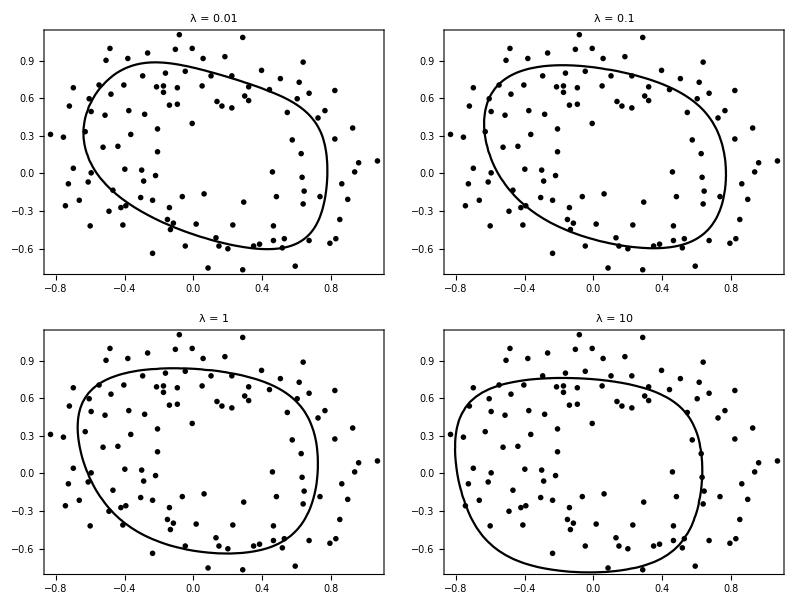

```mathematica
Grid@Partition[Table[Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Axes->False,PlotLabel->StringJoin@{"λ = "  ,ToString@k},ImageSize->280,Frame->True],ContourPlot[Evaluate[θ[k].x1x2==0],{x1,-1,1},{x2,-1,1}]],{k,{0.01,0.1,1,10}}],2]
```

Как мы видим, введение коэффициента регуляризации позволяет избежать эффекта переобучения, но слишком большое его значение ведет к эффекту недообучения. Оптимальное его значение для данной задачи λ≈0.1.

Запишем классифицирующую функцию:

```mathematica
a[θ_,x_]:=(1+Exp[-θ.x])^-1
```

И изобразим график плотности вероятности объектов, которые классифицируются полученным алгоритмом как класс 1:

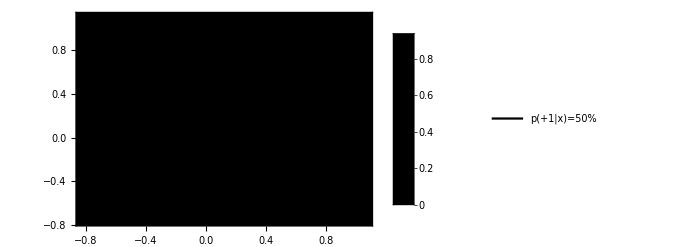

```mathematica
Show[{ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Frame->True,Axes->False,ImageSize->400],DensityPlot[Evaluate[a[θ[0.1],x1x2]],{x1,-2,2},{x2,-2,2},PlotLegends->Automatic,PlotRange->All],ContourPlot[Evaluate[θ[0.1].x1x2==0],{x1,-2,2},{x2,-2,2},PlotLegends->{"p(+1|x)=50%"}]}]
```

В отличии от задачи классификации метрическими методами, где для классификации было необходимо держать всю выборку в памяти, решение данной задачи - n-мерный (n=28) вектор, который используется в скалярном умножении для классификации объекта х, т.е. отпадает необходимость забивать память хранением всей обучающей выборкой.